# NEQ-SR ICS Emittance Degradation

## Units + Constants

```mathematica
(*Units*)
MeV=10^6;
μJ=10^-6;
m=1;
cm=10^-2;
mm=10^-3;
μm=10^-6;
nm=10^-9;
rad=1;
mrad=10^-3;
Hz=1;
MHz=10^6;
nC=10^-9;
pC=10^-12;
ps=10^-12;
```

```mathematica
(*Constants*)
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
echarge=1.60217662*10^-19;
re=2.8179403262*10^-15;
me=0.51099895MeV;
λc=2.42631023867*10^-12;
(*Compton wavelength in m*)
σT=6.65245871548*10^-29;
fivedeg=(5*π)/180;
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## Cases

Baseline MAXIII NEQ-SR ICS parameters for the injection emittance. n_bunch is no. bunches, f_comp is the frequency of the ICS interaction, f_inj is the injection frequency.

```mathematica
baseMAXIIIinj={Ee->700MeV,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,λ->1064nm,σL->25μm,βIP->1m,ϵinj->1.02nm rad,tpulse->5.7ps,σze->0.0266815,θcol->0.1mrad,nbunch->10,fcomp->83.33MHz,finj->25Hz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4,npts->10000};
```

Optimised MAXIII NEQ-SR ICS and CLS-300 Example Source parameters for the injection emittance. - INCORRECT f_rev etc. right now

```mathematica
NEQSRICS={Ee->700MeV,Epulse->120μJ,λ->1064nm,σL->25μm,βIP->1.586m,frev->83.33MHz,finj->25Hz,ϵinj->1.02nm rad,ϕ->fivedeg,Q->0.996nC,tpulse->5.7ps,σze->0.0266815,ΔEe->8.6*10^-4,Δλ->6.57*10^-4,θcol->0.08656mrad,npts->10000};
```

```mathematica
CLS300NdYAG={Ee->99.71MeV,Epulse->100μJ,λ->1064nm,σL->25μm,βIP->5cm,frev->100MHz,finj->25Hz,ϵinj->5.10nm rad,ϕ->0,Q->100pC,tpulse->5ps,σze->3mm,ΔEe->8.6*10^-4,Δλ->6.5*10^-4,θcol->1mrad,npts->10000};
```

## Emittance Degradation Intermediaries

The Rayleigh range z_R could be π or 4π depending on Rod Loewen and Ron Ruth’s choice. t_inj is the time between injection of new bunches. ϵ_(n,inj) is the normalised emittance of the injected electron bunch. f_rev is the revolution frequency of a single electron bunch.

```mathematica
γ[Ee_]:=(Ee+me)/me;
EL[λ_]:=(2*π*hbar*clight)/λ;(*in eV, hbar is in eV, 2π due to hbar*)
zr[λ_,σL_]:=(π*σL^2)/λ;
tinj[finj_]:=1/finj;
ϵninj[ϵinj_,Ee_]:=γ[Ee]*ϵinj;
frev[fcomp_,nbunch_]:=fcomp/nbunch;
```

## Flux + Flux Intermediaries

```mathematica
Xrec[Ee_,λ_]:=(4*γ[Ee]*EL[λ])/me;
σc[Ee_,λ_]:=σT*(1-Xrec[Ee,λ]);
Ne[Q_]:=Q/echarge;
NL[Epulse_,λ_]:=Epulse/(echarge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
σzl[tpulse_]:=clight*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
```

```mathematica
Nγ[Ee_,Q_,Epulse_,λ_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_]:=σc[Ee,λ]*(Ne[Q]*NL[Epulse,λ]*Cos[ϕ/2])/(2*π*convxy[βIP,ϵn,Ee,σL]*Sqrt[convxy[βIP,ϵn,Ee,σL]^2*Cos[ϕ/2]^2+convz[σze,tpulse]^2*Sin[ϕ/2]^2])
```

## Bandwidth + Bandwidth Intermediaries

```mathematica
ψ[Ee_,θcol_]:=γ[Ee]*θcol;
```

```mathematica
(*Individual Terms*)
collterm[Ee_,λ_,θcol_]:=1/Sqrt[12]*ψ[Ee,θcol]^2/(1+Xrec[Ee,λ]+ψ[Ee,θcol]^2/2);
beamspreadterm[Ee_,λ_,ΔEe_,θcol_]:=(2+Xrec[Ee,λ])/(1+Xrec[Ee,λ]+ψ[Ee,θcol]^2)*ΔEe;
laserspreadterm[Ee_,λ_,Δλ_,θcol_]:=(1+ψ[Ee,θcol]^2)/(1+Xrec[Ee,λ]+ψ[Ee,θcol]^2)*Δλ;
emitterm[Ee_,ϵn_,βIP_]:=(2*γ[Ee]*ϵn)/βIP;
```

```mathematica
(*Bandwidth*)
ΔEγ[Ee_,λ_,θcol_,ΔEe_,Δλ_,ϵn_,βIP_]:=Sqrt[collterm[Ee,λ,θcol]^2+beamspreadterm[Ee,λ,ΔEe,θcol]^2+laserspreadterm[Ee,λ,Δλ,θcol]^2+emitterm[Ee,ϵn,βIP]^2];
```

## Interactions per Electron (Upper Bound)

Calculation of the integrated flux within a single electron. Assumes no flux degradation throughout the interaction.

```mathematica
Fint[Ee_,Q_,Epulse_,λ_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_,fcomp_,finj_]:=Nγ[Ee,Q,Epulse,λ,ϕ,βIP,ϵn,σL,σze,tpulse]*fcomp*tinj[finj];
```

```mathematica
Fint[Ee,Q,Epulse,λ,ϕ,βIP,ϵninj[ϵinj,Ee],σL,σze,tpulse,fcomp,finj]/.baseMAXIIIinj
```

2.9394×10^9

Total no. electrons in the accelerator.

```mathematica
Netot[Q_,nbunch_]:=Ne[Q]*nbunch;
```

```mathematica
Netot[Q,nbunch]/.baseMAXIIIinj
```

6.21654×10^10

Average no. ICS interactions per electron. Upper bound as we assume the flux is constant throughout the interaction, i.e emittance stays at injected value.

```mathematica
ncomp[Ee_,Q_,Epulse_,λ_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_,fcomp_,finj_,nbunch_]:=Fint[Ee,Q,Epulse,λ,ϕ,βIP,ϵn,σL,σze,tpulse,fcomp,finj]/Netot[Q,nbunch];
```

```mathematica
ncomp[Ee,Q,Epulse,λ,ϕ,βIP,ϵninj[ϵinj,Ee],σL,σze,tpulse,fcomp,finj,nbunch]/.baseMAXIIIinj
```

0.0472835

## Energy Loss Per Electron via ICS Interaction

The average energy loss of an electron because of the ICS interaction. This requires z_R > > t_pulse as trests the photon emission as weak undulator radiation.

```mathematica
ΔE[Ee_,λ_,σL_,Epulse_]:=1/echarge*(32*π)/3*re^2*γ[Ee]^2*Epulse/(zr[λ,σL]*λ);(*in eV*)
```

```mathematica
ΔE[Ee,λ,σL,Epulse]/.baseMAXIIIinj
```

190.754

The energy loss per electron increases substantially ΔE ∝ γ^2 with electron energy. Hence, this may only be a phenomena in high energy electron machines.

## No. Turns to Radiate e^- Initial Energy

No. turns that are required to completely damp away the initial energy of the electron. This is

```mathematica
nd[Ee_,λ_,σL_,Epulse_]:=Ee/ΔE[Ee,λ,σL,Epulse];
```

```mathematica
nd[Ee,λ,σL,Epulse]/.baseMAXIIIinj
```

3.66965×10^6

## Transverse Damping Time

The transverse damping time is the time it takes to radiate away the initial electron energy.

```mathematica
τxy[Ee_,λ_,σL_,Epulse_,fcomp_,nbunch_]:=Ee/ΔE[Ee,λ,σL,Epulse]*1/frev[fcomp,nbunch];
```

```mathematica
τxy[Ee,λ,σL,Epulse,fcomp,nbunch]/.baseMAXIIIinj
```

0.440376

## Average Transverse Normalised Emittance Diffusion per Turn due to ICS

The average increase in the emittance per turn due to the ICS interaction.

```mathematica
Δϵn[λ_,Ee_,σL_,Epulse_,βIP_]:=3/10*λc/λ*ΔE[Ee,λ,σL,Epulse]/Ee*βIP;
```

```mathematica
Δϵn[λ,Ee,σL,Epulse,βIP]/.baseMAXIIIinj
```

1.86424×10^-13

## Average Quantum Excitation Rate of Emittance due to ICS

Rate of emittance change due to the quantum excitation of the emittance by the ICS interaction. The change of emittance of a single bunch per unit time.

```mathematica
dϵndt[λ_,Ee_,σL_,Epulse_,βIP_,fcomp_,nbunch_]:=Δϵn[λ,Ee,σL,Epulse,βIP]*frev[fcomp,nbunch];
```

```mathematica
dϵndt[λ,Ee,σL,Epulse,βIP,fcomp,nbunch]/.baseMAXIIIinj
```

1.55347×10^-6

## Emittance Degradation at Re-Injection Time

The total emittance change via quantum excitation from the ICS interaction before the bunch is dumped.

```mathematica
Δϵnreinj[λ_,Ee_,σL_,Epulse_,βIP_,fcomp_,nbunch_,finj_]:=dϵndt[λ,Ee,σL,Epulse,βIP,fcomp,nbunch]*tinj[finj];
```

```mathematica
Δϵnreinj[λ,Ee,σL,Epulse,βIP,fcomp,nbunch,finj]/.baseMAXIIIinj
```

6.21387×10^-8

## Emittance Parameters

```mathematica
Grid[{{"MAXIII NEQ-SR ICS: Baseline Configuration",SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Parameter","Symbol","Value", "Unit"},{"Average Electron Interactions Per Injection",",⟨n_comp⟩",ncomp[Ee,Q,Epulse,λ,ϕ,βIP,ϵninj[ϵinj,Ee],σL,σze,tpulse,fcomp,finj,nbunch]/.baseMAXIIIinj,""},{"Transverse Damping Time", "τ_(x, y)",τxy[Ee,λ,σL,Epulse,fcomp,nbunch]/.baseMAXIIIinj,"s"},{"No. Turns to Damp", "n_d",nd[Ee,λ,σL,Epulse]/.baseMAXIIIinj,"turns"},{"Normalised Injected Emittance","ϵ_(n, inj)",ϵninj[ϵinj,Ee]/(mm mrad)/.baseMAXIIIinj,"mm-mrad"},{"Normalised Emittance at Re-Injection","ϵ_(n, re - inj)",(ϵninj[ϵinj,Ee]+Δϵnreinj[λ,Ee,σL,Epulse,βIP,fcomp,nbunch,finj])/(mm mrad)/.baseMAXIIIinj,"mm-mrad"},{"Emittance Change (Injection to Re-Injection)","Δϵ_(n, (inj  -  re - inj))",Δϵnreinj[λ,Ee,σL,Epulse,βIP,fcomp,nbunch,finj]/(mm mrad)/.baseMAXIIIinj,"mm-mrad"},{"Average Quantum Excitation Rate of Emittance","⟨dϵ_n/dt⟩",dϵndt[λ,Ee,σL,Epulse,βIP,fcomp,nbunch]/(mm mrad)/.baseMAXIIIinj,"mm-mrad/s"},{"Average Transverse Normalised Emittance Diffusion per Turn", "Δϵ_n",Δϵn[λ,Ee,σL,Epulse,βIP]/(mm mrad)/.baseMAXIIIinj,"mm-mrad/turn"},{"Flux Degradation via Emittance Degradation","ΔF_ϵ_n",baseMAXIIIinjFluxLoss,"%"}},Dividers->{{True,True,True,True,True},{True,True,True,False,False,False,False,False,False,False,False,True}}]
```

MAXIII NEQ-SR ICS: Baseline Configuration |  |  | 
Parameter | Symbol | Value | Unit
Average Electron Interactions Per Injection | ,⟨n_comp⟩ | 0.0472835 | 
Transverse Damping Time | τ_(x, y) | 0.440376 | s
No. Turns to Damp | n_d | 3.66965×10^6 | turns
Normalised Injected Emittance | ϵ_(n, inj) | 1.39828 | mm-mrad
Normalised Emittance at Re-Injection | ϵ_(n, re - inj) | 1.46042 | mm-mrad
Emittance Change (Injection to Re-Injection) | Δϵ_(n, (inj  -  re - inj)) | 0.0621387 | mm-mrad
Average Quantum Excitation Rate of Emittance | ⟨dϵ_n/dt⟩ | 1.55347 | mm-mrad/s
Average Transverse Normalised Emittance Diffusion per Turn | Δϵ_n | 1.86424×10^-7 | mm-mrad/turn
Flux Degradation via Emittance Degradation | ΔF_ϵ_n | 0.680369 | %

## Emittance Plots

```mathematica
ϵnvst[ϵinj_,Ee_,λ_,σL_,Epulse_,βIP_,fcomp_,nbunch_,t_]:=ϵninj[ϵinj,Ee]+t*dϵndt[λ,Ee,σL,Epulse,βIP,fcomp,nbunch];
```

```mathematica
baseMAXIIIinjϵnvst=Table[{t,ϵnvst[ϵinj,Ee,λ,σL,Epulse,βIP,fcomp,nbunch,t]/(mm mrad)/.baseMAXIIIinj},{t,0,tinj[finj]/.baseMAXIIIinj,tinj[finj]/npts/.baseMAXIIIinj}];
```

```mathematica
ϵnvsturn[ϵinj_,Ee_,λ_,σL_,Epulse_,βIP_,nturn_]:=ϵninj[ϵinj,Ee]+nturn*Δϵn[λ,Ee,σL,Epulse,βIP];
```

```mathematica
baseMAXIIIinjϵnvsturn=Table[{nturn/10^6,ϵnvsturn[ϵinj,Ee,λ,σL,Epulse,βIP,nturn]/(mm mrad)/.baseMAXIIIinj},{nturn,0,fcomp/finj/.baseMAXIIIinj,fcomp/(finj*npts)/.baseMAXIIIinj}];
```

```mathematica
ϵntimeplot=ListLinePlot[baseMAXIIIinjϵnvst,Frame->True,LabelStyle->15,PlotLabel->"Baseline MAXIII NEQ-SR ICS ϵ_n Degradation",FrameLabel->{"Time t (s)","Normalised Emittance ϵ_n (mm-mrad)"},PlotLegends->Placed[LineLegend[{"MAXIII NEQ-SR ICS","CLS-300"},LabelStyle->12,LegendFunction->frame],{0.7,0.2}]];
```

```mathematica
ϵnturnplot=ListLinePlot[baseMAXIIIinjϵnvsturn,Frame->True,LabelStyle->15,PlotLabel->"Baseline MAXIII NEQ-SR ICS ϵ_n Degradation",FrameLabel->{"No. Turns n_turn (10^6)","Normalised Emittance ϵ_n (mm-mrad)"},PlotLegends->Placed[LineLegend[{"MAXIII NEQ-SR ICS","CLS-300"},LabelStyle->12,LegendFunction->frame],{0.7,0.2}]];
```

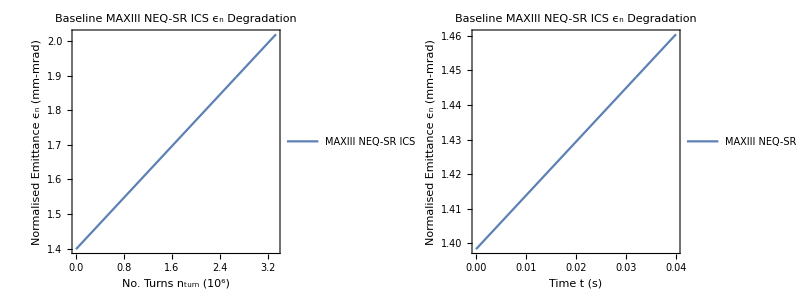

```mathematica
Grid[{{ϵnturnplot,ϵntimeplot}}]
```

The MAXIII NEQ-SR ICS has a much greater rate of emittance degradation as the energy loss per electron increases substantially ΔE ∝ γ^2. CLS-300 has a higher rep rate hence the more turns.

## Flux Degradation

```mathematica
FluxperBunchInjection=Nγ[Ee,Q,Epulse,λ,ϕ,βIP,ϵninj[ϵinj,Ee],σL,σze,tpulse]/.baseMAXIIIinj
```

881.854

```mathematica
FluxperBunchReInjection=Nγ[Ee,Q,Epulse,λ,ϕ,βIP,(ϵninj[ϵinj,Ee]+Δϵnreinj[λ,Ee,σL,Epulse,βIP,fcomp,nbunch,finj]),σL,σze,tpulse]/.baseMAXIIIinj
```

869.935

```mathematica
baseMAXIIIinjFluxNoDegrade=Table[{t,FluxperBunchInjection},{t,0,tinj[finj]/.baseMAXIIIinj,tinj[finj]/npts/.baseMAXIIIinj}];
```

```mathematica
baseMAXIIIinjFluxperBunchvsTime=Table[{t,Nγ[Ee,Q,Epulse,λ,ϕ,βIP,ϵnvst[ϵinj,Ee,λ,σL,Epulse,βIP,fcomp,nbunch,t],σL,σze,tpulse]/.baseMAXIIIinj},{t,0,tinj[finj]/.baseMAXIIIinj,tinj[finj]/npts/.baseMAXIIIinj}];
```

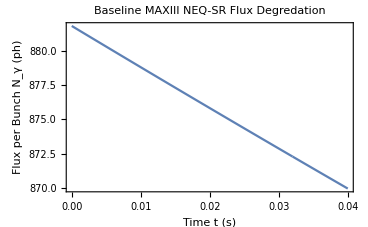

```mathematica
ListLinePlot[baseMAXIIIinjFluxperBunchvsTime,Frame->True,LabelStyle->15,PlotLabel->"Baseline MAXIII NEQ-SR Flux Degredation",FrameLabel->{"Time t (s)","Flux per Bunch N_γ (ph)"}]
```

## Fractional Flux Loss via Emittance Degradation

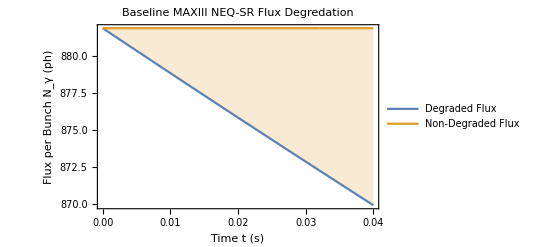

```mathematica
ListLinePlot[{baseMAXIIIinjFluxperBunchvsTime,baseMAXIIIinjFluxNoDegrade},Frame->True,LabelStyle->15,PlotLabel->"Baseline MAXIII NEQ-SR Flux Degredation",FrameLabel->{"Time t (s)","Flux per Bunch N_γ (ph)"},Filling->{2->{1}},PlotLegends->Placed[LineLegend[{"Degraded Flux","Non-Degraded Flux"},LabelStyle->12,LegendFunction->frame],{0.3,0.2}]]
```

```mathematica
baseMAXIIIinjintFluxNoDeg=Integrate[Interpolation[baseMAXIIIinjFluxNoDegrade][t],{t,0,tinj[finj]/.baseMAXIIIinj}];
baseMAXIIIinjintFluxDeg=Integrate[Interpolation[baseMAXIIIinjFluxperBunchvsTime][t],{t,0,tinj[finj]/.baseMAXIIIinj}];
baseMAXIIIinjFluxLoss=(baseMAXIIIinjintFluxNoDeg-baseMAXIIIinjintFluxDeg)/baseMAXIIIinjintFluxNoDeg*100
```

0.680369

The flux loss of 0.68% is a very small flux depreciation. Emittance degradation factor is a cause of concern only for high energy γ-ray ICS, remember this is for 8 MeV γ-rays, at 40 MeV γ-rays this may be prohibitive. To mitigate this we could re-inject at a higher frequency.

## Bandwidth Growth

```mathematica
baseMAXIIIinjΔEγvst=Table[{t,100*ΔEγ[Ee,λ,θcol,ΔEe,Δλ,ϵnvst[ϵinj,Ee,λ,σL,Epulse,βIP,fcomp,nbunch,t],βIP]/.baseMAXIIIinj},{t,0,tinj[finj]/.baseMAXIIIinj,tinj[finj]/npts/.baseMAXIIIinj}];
```

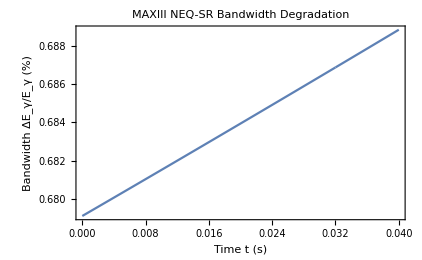

```mathematica
ListLinePlot[baseMAXIIIinjΔEγvst,Frame->True,LabelStyle->15,PlotLabel->"MAXIII NEQ-SR Bandwidth Degradation",FrameLabel->{"Time t (s)","Bandwidth ΔE_γ/E_γ (%)"}]
```